```mathematica
G0 [α_,x_]:=1*ⅇ^(-α*x*10^-4);
```

Normalized generation and units converted to microns in exponential

```mathematica
Subscript[α, 650]=2810;Subscript[α, 550]=6390; Subscript[α, 450]=25500; Subscript[α, 1100]=3.5;
```

```mathematica
G0[Subscript[α, 650],20.0]
```

0.00362464

```mathematica
G0[Subscript[α, 1100],10]
```

0.996506

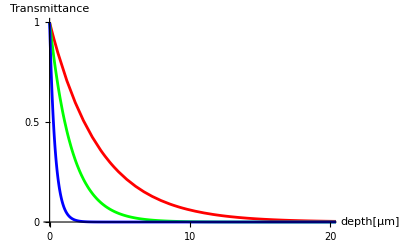

```mathematica
Plot[{G0[Subscript[α, 650],x],G0[Subscript[α, 550],x],G0[Subscript[α, 450],x]},{x,0,30}, AxesLabel->{"depth[μm]","Transmittance"},PlotRange->{{0,20},{0,1}}, AspectRatio->1/GoldenRatio,PlotStyle->{{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Blue,Thickness[0.005]}},Ticks->{{0,10,20},{0,.5,1}},AxesStyle->Directive[Gray,12]]
```

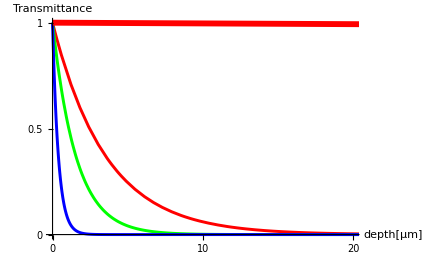

```mathematica
Plot[{G0[Subscript[α, 650],x],G0[Subscript[α, 550],x],G0[Subscript[α, 450],x],G0[Subscript[α, 1100],x]},{x,0,30}, AxesLabel->{"depth[μm]","Transmittance"},PlotRange->{{0,20},{0,1}}, AspectRatio->1/GoldenRatio,PlotStyle->{{Red,Thickness[0.005]},{Green,Thickness[0.005]},{Blue,Thickness[0.005]},{Red,Thickness[0.01]}},Ticks->{{0,10,20},{0,.5,1}},AxesStyle->Directive[Gray,12]]
```